```mathematica
(* Initialization stuff; of no intrinsic interest *)
ClearAll["Global`*"];
If[Length[$FrontEnd] > 0,NBDir=SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
(* If running from shell, must start from inside same directory in which notebook resides *)
If[$VersionNumber<8,(*then*) Print["These programs require Mathematica version 8 or greater."];Abort[]];
(* Method of displaying figures depends on whether being run in batch mode or interactively *)
If[$FrontEnd == Null,OpenFigsUsingShell=True,OpenFigsUsingShell=False]; 
(* Current working directory should correspond to appropriate location now whether running from shell or notebook *)
Get["/Volumes/Data/Code/Mathematica/Autoload/init.m"];
```

```mathematica
𝓇=0.05;
ℛ=1+𝓇;
𝓅=1.;
𝒶Bar=𝒶=𝒷Bar=𝒷={0.,0.};
𝓂Bar=𝓂=𝒸Bar=𝒸=𝒸Rat={1.,1.};
𝓍=𝓍Bar={0.,0.};
λ=0.5;
AddPeriod[θVal_]:=Block[{},
AppendTo[𝒷,ℛ Last[𝒶]];
AppendTo[𝒷Bar,ℛ Last[𝒶Bar]];
AppendTo[𝓍,𝒷[[-1]]+𝓅 (θVal-1)];
AppendTo[𝓍Bar,𝒷Bar[[-1]]+ 𝓅 (θVal-1)];
AppendTo[𝒸,𝓅 + (𝓇/ℛ)𝓍[[-1]]];
AppendTo[𝒸Rat,𝓅+(𝓇/ℛ)𝓍Bar[[-1]]];
AppendTo[𝒸Bar,λ 𝒸Rat[[-1]]+(1-λ)𝒸Bar[[-1]]];
AppendTo[𝓂,𝓍[[-1]]+𝓅];
AppendTo[𝓂Bar,𝓍Bar[[-1]]+𝓅];
AppendTo[𝒶,𝓂[[-1]]-𝒸[[-1]]];
AppendTo[𝒶Bar,𝓂Bar[[-1]]-𝒸Bar[[-1]]];
𝒸𝒸=Take[𝒸,Length[𝒸]-1];
𝒸𝒸Bar=Take[𝒸Bar,Length[𝒸Bar]-1];
𝒶𝒶=Take[𝒶,Length[𝒶]-1];
𝒶𝒶Bar=Take[𝒶,Length[𝒶Bar]-1];
];
AddPeriod[2];
Do[AddPeriod[1],{10}];
```

```mathematica
𝒷
```

{0.,0.,0.}

```mathematica
𝒸
```

{1.,1.,1.04762}

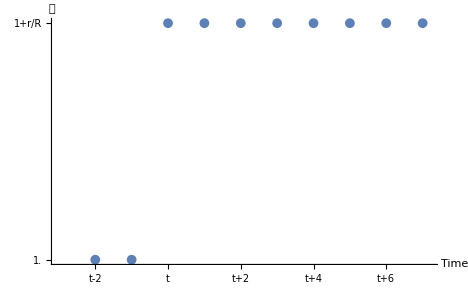

```mathematica
Print[cPlot=ListPlot[𝒸,Ticks->{{{1,"t-2"},{2,"t-1"},{3,"t"},{4,"t+1"},{5,"t+2"},{6,"t+3"},{7,"t+4"},{8,"t+5"},{9,"t+6"},{10,"t+7"}},{{1+(0.0001 𝓇)/ℛ,"1."},{1+𝓇/ℛ,"1+r/R"}}},PlotRange->{{0,10.2},Automatic},AxesLabel->{"Time","𝒞"},PlotStyle->PointSize[0.015]]];
```

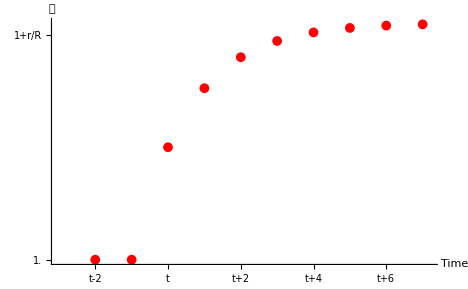

```mathematica
Print[cBarPlot=ListPlot[𝒸Bar,Ticks->{{{1,"t-2"},{2,"t-1"},{3,"t"},{4,"t+1"},{5,"t+2"},{6,"t+3"},{7,"t+4"},{8,"t+5"},{9,"t+6"},{10.,"t+7"}},{{1+0.0001 𝓇/ℛ,"1."},{1+(𝓇/ℛ),"1+r/R"}}}
,PlotRange->{{0,10.2},Automatic}
,AxesLabel->{"Time","𝒞"}
,PlotStyle->{PointSize[0.015],RGBColor[1,0,0]}
]];
```

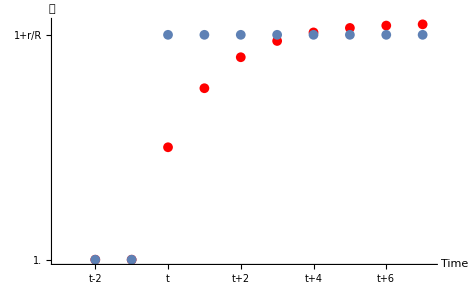

```mathematica
Print[StickyExpectationsCc=Show[cBarPlot,cPlot]];
```

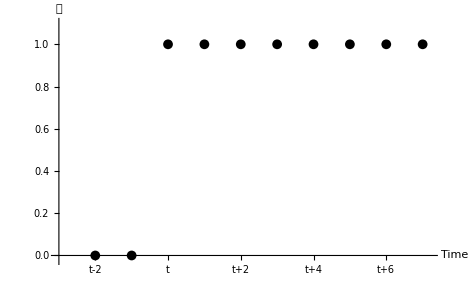

```mathematica
Print[xPlot=ListPlot[𝓍,Ticks->{{{1,"t-2"},{2,"t-1"},{3,"t"},{4,"t+1"},{5,"t+2"},{6,"t+3"},{7,"t+4"},{8,"t+5"},{9,"t+6"},{10.,"t+7"}},Automatic}
,PlotRange->{{0,10.2},{-0.02,1.1}}
,AxesOrigin->{0.,0.}
,PlotStyle->{PointSize[0.015],RGBColor[0,0,0]}
,AxesLabel->{"Time","𝓍"}
]];
```

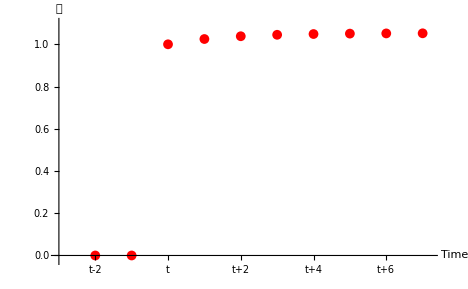

```mathematica
Print[xBarPlot=ListPlot[𝓍Bar,Ticks->{{{1,"t-2"},{2,"t-1"},{3,"t"},{4,"t+1"},{5,"t+2"},{6,"t+3"},{7,"t+4"},{8,"t+5"},{9,"t+6"},{10.,"t+7"}},Automatic}
,PlotRange->{{0,10.2},{-0.02,1.1}}
,AxesOrigin->{0.,0.}
,AxesLabel->{"Time","𝓍"}
,PlotStyle->{PointSize[0.015],RGBColor[1,0,0]}
]];
```

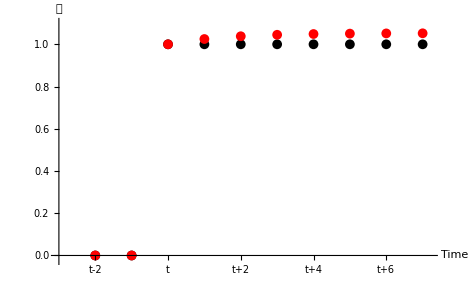

```mathematica
Print[Show[xPlot,xBarPlot]];
```

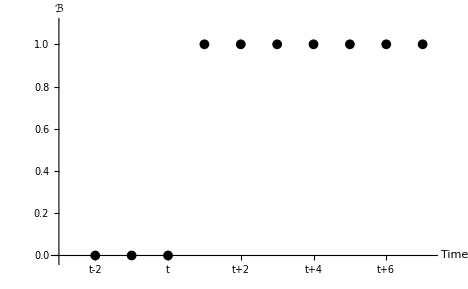

```mathematica
Print[bPlot=ListPlot[𝒷,Ticks->{{{1,"t-2"},{2,"t-1"},{3,"t"},{4,"t+1"},{5,"t+2"},{6,"t+3"},{7,"t+4"},{8,"t+5"},{9,"t+6"},{10.,"t+7"}},Automatic}
,PlotRange->{{0,10.2},{-0.02,1.1}}
,AxesOrigin->{0.,0.}
,AxesLabel->{"Time","ℬ"},PlotStyle->{PointSize[0.015],RGBColor[0,0,0]}]];
```

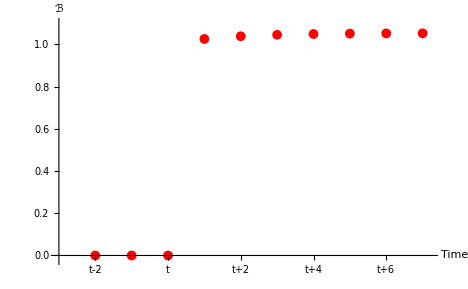

```mathematica
Print[bBarPlot=ListPlot[𝒷Bar,Ticks->{{{1,"t-2"},{2,"t-1"},{3,"t"},{4,"t+1"},{5,"t+2"},{6,"t+3"},{7,"t+4"},{8,"t+5"},{9,"t+6"},{10,"t+7"}},Automatic}
,PlotRange->{{0,10.2},{-0.02,1.1}}
,AxesOrigin->{0.,0.}
,AxesLabel->{"Time","ℬ"}
,PlotStyle->{PointSize[0.015],RGBColor[1,0,0]}
]];
```

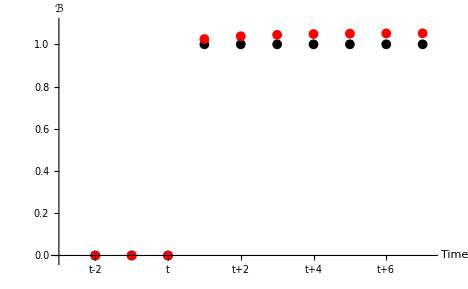

```mathematica
Print[StickyExpectationsCb = Show[bPlot,bBarPlot,BaseStyle->{FontSize->14}]];
```

```mathematica
ExportFigsToDir["bPlot","../../Figures"];
ExportFigsToDir["cPlot","../../Figures"];
ExportFigsToDir["StickyExpectationsCb","../../Figures"];
ExportFigsToDir["StickyExpectationsCc","../../Figures"];
```

-Graphics-

Exporting figure to ../../Figures/bPlot.pdf

-Graphics-

Exporting figure to ../../Figures/cPlot.pdf

-Graphics-

Exporting figure to ../../Figures/StickyExpectationsCb.pdf

-Graphics-

Exporting figure to ../../Figures/StickyExpectationsCc.pdf